```mathematica
SetDirectory["/home/runbo/Desktop/Summer_Research/AOD_Files/"]
Clear[fileName]
fileName=FileNames["*"];
size=fileName//Length
```

/home/runbo/Desktop/Summer_Research/AOD_Files

255

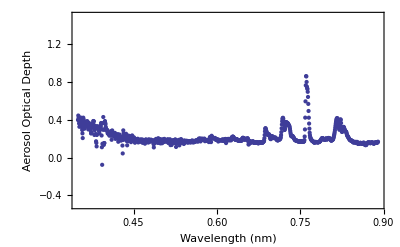

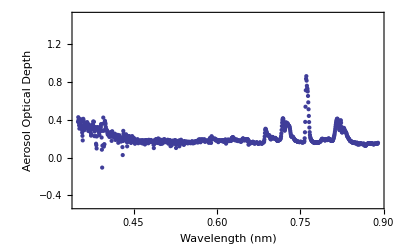

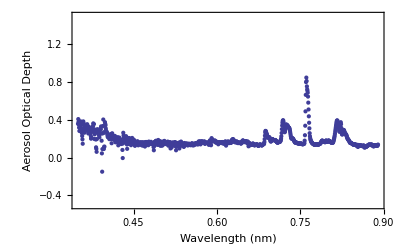

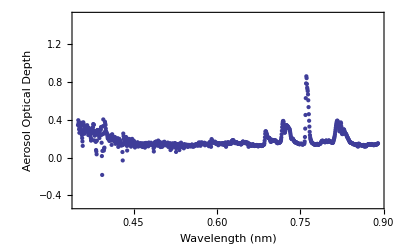

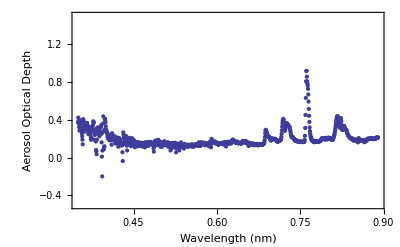

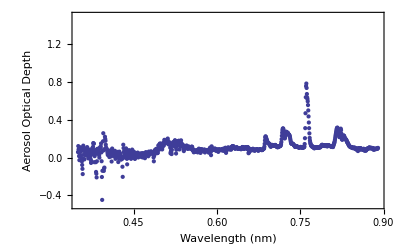

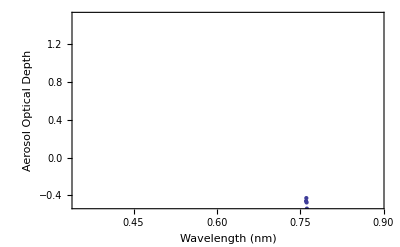

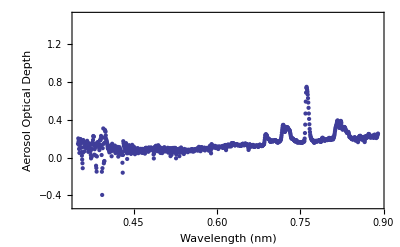

-Graphics-

-Graphics-

-Graphics-

«124 more identical outputs»

```mathematica
For[i=0, i<size, i++, data=Import[fileName[[i+1]]];
Print[ListPlot[data, PlotRange->{{0.35,0.89},{-0.5,1.5}},Frame->True, FrameLabel->{"Wavelength (nm)", "Aerosol Optical Depth", fileName[[i+1]], ""}]]]
```